```mathematica
ariasD[0] = 1;
ariasD[n_Integer?Positive] := ariasD[n] = Sum[2^((k (k - 1) - n (n - 1))/2) ariasD[k]/(n - k + 1)!, {k, 0, n - 1}]/(2^n - 1);
iFabiusF[x_] := Module[{prec = Precision[x], n, p, q, s, tol, w, y, z},
  If[x < 0, Return[0, Module]]; tol = 10^(-prec);
  z = SetPrecision[x, Infinity]; s = 1; y = 0;
  z = If[0 <= z <= 2, 1 - Abs[1 - z],
    q = Quotient[z, 2];
    If[ThueMorse[q] == 1, s = -1];
    1 - Abs[1 - z + 2 q]];
  While[z > 0,
   n = -Floor[RealExponent[z, 2]]; p = 2^n;
   z -= 1/p; w = 1;
   Do[w = ariasD[m] + p z w/(n - m + 1); p /= 2, {m, n}];
   y = w - y;
   If[Abs[w] < Abs[y] tol, Break[]]];
  SetPrecision[s Abs[y], prec]]
FabiusF[Infinity] = Interval[{-1, 1}];
FabiusF[x_?NumberQ] /; If[Im[x] == 0, TrueQ[Composition[BitAnd[#, # - 1] &, Denominator][x] == 0], False] := iFabiusF[x]
Derivative[n_Integer][FabiusF] := 2^(n (n + 1)/2) FabiusF[2^n #] &
SetAttributes[FabiusF, {NumericFunction, Listable}];
```

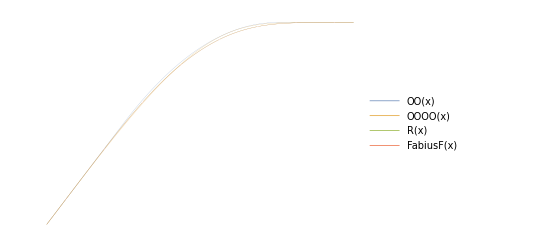
OO[3/4]= | 15/16
0.9375
OOOO[3/4]= | 0.935031
0.935031
R[3/4]= | 715/768
0.93099
FabiusF[3/4]= | 67/72
0.930556
{-Graphics-}

```mathematica
T=4;
A0[x_]:=(Max[x,0]^T)/T!;
A1[x_]:=2^1 (A0[x]-A0[(x-1/2^1)]);
A2[x_]:=2^2 (A1[x]-A1[(x-1/2^2)]);
A3[x_]:=2^3 (A2[x]-A2[(x-1/2^3)]);
A4[x_]:=2^4 (A3[x]-A3[(x-1/2^4)]);
A5[x_]:=2^5 (A4[x]-A4[(x-1/2^5)]);
A6[x_]:=2^6 (A5[x]-A5[(x-1/2^6)]);
A7[x_]:=2^7 (A6[x]-A6[(x-1/2^7)]);
A8[x_]:=2^8 (A7[x]-A7[(x-1/2^8)]);
A9[x_]:=2^9 (A8[x]-A8[(x-1/2^9)]);
A10[x_]:=2^10 (A9[x]-A9[(x-1/2^10)]);
A11[x_]:=2^11 (A10[x]-A10[(x-1/2^11)]);
A12[x_]:=2^12 (A11[x]-A11[(x-1/2^12)]);
A13[x_]:=2^13 (A12[x]-A12[(x-1/2^13)]);
A14[x_]:=2^14 (A13[x]-A13[(x-1/2^14)]);
A15[x_]:=2^15 (A14[x]-A14[(x-1/2^15)]);
A16[x_]:=2^16 (A15[x]-A15[(x-1/2^16)]);
A17[x_]:=2^17 (A16[x]-A16[(x-1/2^17)]);
A18[x_]:=2^18 (A17[x]-A17[(x-1/2^18)]);
A19[x_]:=2^19 (A18[x]-A18[(x-1/2^19)]);
A20[x_]:=2^20 (A19[x]-A19[(x-1/2^20)]);
A21[x_]:=2^21 (A20[x]-A20[(x-1/2^21)]);
A22[x_]:=2^22 (A21[x]-A21[(x-1/2^22)]);
A23[x_]:=2^23 (A22[x]-A22[(x-1/2^23)]);
A24[x_]:=2^24 (A23[x]-A23[(x-1/2^24)]);
A25[x_]:=2^25 (A24[x]-A24[(x-1/2^25)]);
A26[x_]:=2^26 (A25[x]-A25[(x-1/2^26)]);
A27[x_]:=2^27 (A26[x]-A26[(x-1/2^27)]);
A28[x_]:=2^28 (A27[x]-A27[(x-1/2^28)]);
A29[x_]:=2^29 (A28[x]-A28[(x-1/2^29)]);
A30[x_]:=2^30 (A29[x]-A29[(x-1/2^30)]);
A31[x_]:=2^31 (A30[x]-A30[(x-1/2^31)]);
A32[x_]:=2^32 (A31[x]-A31[(x-1/2^32)]);
R[x_]:=A4[(x-1/2^(T+1))];
(*ToUpperCase[StringReplace[StringReplace[StringReplace[ToString[R[x],InputForm],"["->"("],"]"->")"]," "-> ""]]*)
(*ToUpperCase[StringReplace[StringReplace[StringReplace[ToString[Simplify[R[x]],InputForm],"["->"("],"]"->")"]," "-> ""]]*)
OO[x_]:=(1/32)*((1-8*(x-1))*Abs[1-8*(x-1)]+(8*(x-1)+7)*Abs[8*(x-1)+7]-(8*(x-1)+5)*Abs[8*(x-1)+5]-(8*(x-1)+3)*Abs[8*(x-1)+3]+(8*(x-1)+1)*Abs[8*(x-1)+1]-(3-8*(x-1))*Abs[3-8*(x-1)]-(5-8*(x-1))*Abs[5-8*(x-1)]+(7-8*(x-1))*Abs[7-8*(x-1)]);
OOOO[x_]:=-((0-(-1)^Floor[x/1+0.]*(Exp[-(1/(x-1*Floor[x/1]))]/(Exp[-(1/(x-1*Floor[x/1]))]+Exp[-(1/(1-(x-1*Floor[x/1])))]))+(-1)^Floor[x/1+0.]*(Exp[-(1/(1-(x-1*Floor[x/1])))]/(Exp[-(1/(x-1*Floor[x/1]))]+Exp[-(1/(1-(x-1*Floor[x/1])))])))/2)+0.5;
Column[{
TableForm[{
{"OO[3/4]=" ,{OO[3/4],N[OO[3/4]]}},
{"OOOO[3/4]=" ,{OOOO[3/4],N[OOOO[3/4]]}},
{"R[3/4]=" ,{R[3/4],N[R[3/4]]}},
{"FabiusF[3/4]=" ,{FabiusF[3/4],N[FabiusF[3/4]]}}
}],
{Plot[{OO[x],OOOO[x],R[x],FabiusF[x]},{x,0.5,1},WorkingPrecision->MachinePrecision,ImageSize->Full,Axes->False,MaxRecursion->0,PlotPoints->1+2^8,PlotStyle->Thickness[0.00001],PlotLegends-> Placed["Expressions",{Center,Top}],PlotRangePadding->0]}},Center]
```